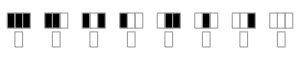
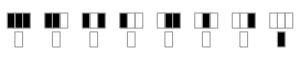
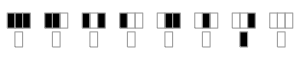
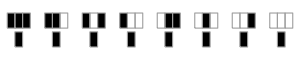
-Graphics-
00000000=0
-Graphics-
00000001=1
-Graphics-
00000010=2
 . . . 
-Graphics-
11111111=255

```mathematica
Column[Insert[
Column[{RulePlot[CellularAutomaton[#],],Row[Text/@Flatten[Append[IntegerDigits[#,2,8],{"=",ToString[#]}]],Spacer[24]]}]&/@{0,1,2,255},
Rotate[" . . . ",π/2],-2],]
```